```mathematica
Clear["Global`*"]
SeedRandom[124];

βOLS={1/3,0.75};

kmax=2.3;
kmin=0;
dk=-0.01;

b1min=0;
b1max=0.8;
db1=0.0025;
b2min=0;
b2max=0.8;
db2=0.0025;

S[b_]:=-b.βOLS+1/2b.b;
normq[x_,y_,q_]:=(Abs[x]^q+Abs[y]^q)^(1/q)

b1=Table[i,{i,b1min,b1max,db1}];
b2=Table[i,{i,b2min,b2max,db2}];

L=Table[0,{Length[b1]},{Length[b2]}];
For[i=1,i≤Length[b1],i++,
For[j=1,j≤Length[b1],j++,
L[[i,j]]=S[{b1[[i]],b2[[j]]}]
]
]

q=0.5;

ks=Table[i,{i,kmax,kmin,dk}];

plts=Table[
z=Outer[(Abs[#1]^q+Abs[#2]^q)^(1/q) &,b1,b2];
pos=Position[z,_?(#≤k&)];

Ltest=Table[0,Length[pos]]//Quiet;
For[i=1,i≤Length[Ltest],i++,
pos1=pos[[i]][[1]]//Quiet;
pos2=pos[[i]][[2]]//Quiet;
Ltest[[i]]=L[[pos1,pos2]]//Quiet
];

minpos=Position[Ltest,Min[Ltest]]//Flatten;
minposx=(pos[[minpos]]//Flatten)[[1]]//Quiet;
minposy=(pos[[minpos]]//Flatten)[[2]]//Quiet;
a=b1[[minposx]]//Quiet;
b=b2[[minposy]]//Quiet;

p0=ContourPlot[{
normq[x,y,q]
},
{x,b1min,b1max},
{y,b2min,b2max},
ContourStyle->None ,(*Directive[Thick],*)
Contours->{k},
ColorFunction->(If[#1>0,None,{Opacity[0.3,Orange]}]&),
Method->{"TransparentPolygonMesh"->True}
];

pl=ListContourPlot[Transpose[L],
FrameLabel->{Subscript["β",1],Subscript["β",2]},
DataRange->{{b1min,b1max},{b2min,b2max}},
ContourShading->None,
ContourStyle->Directive[Thick],
Contours->Function[{min,max},Range[min,max,0.1]]
];

Show[p0, pl,
PlotLabel->"k = "<>ToString[PaddedForm[k,{3,3}]]<>", q = "<>ToString[q],
Epilog->{
PointSize[0.03],Red,Point[βOLS],Black,Text[Superscript["β",OLS],βOLS*1.04],
PointSize[0.03],Red,Point[{a,b}],Black,Text[Superscript["β","("<>ToString[q]<>", λ)"], {a+0.1,b} ]
},
Frame->False,
Axes->True],
{k,kmax,kmin,dk}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["../img/gif/animation_q"<>ToString[q]<>"_norm.gif",plts,"AnimationRepetitions"->∞,ImageResolution->100]
```

../img/gif/animation_q0.5_norm.gif

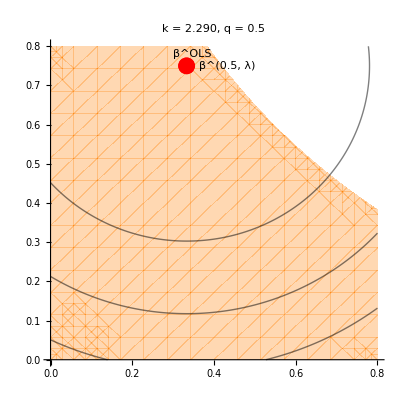
ListAnimate[-Graphics-,{2,1,231,1}]

```mathematica
ListAnimate[plts[[i]],{i,1,Length[ks],1}]
```

```mathematica
k=20;
If[Mod[k, 10] == 0, Print[k], ""];
```

20